# Bound Reference

## General Stuff *

### General commands

```mathematica
(*
1 equal sign ( = ) will permanantly define a variable eg.(x=4) 

putting a ( ,x ) shows that you are solving for x

to clear the variable input (Clear[x]) using the double equals sign ( == ) lets mathmatica know that the two sides are equal but only for that operation 

When multiplying letters together, put a multiplication symobol between them

(* Putting bracket asteric means it is just text, not calculation*)

Putting these commands behind your equation will put it into a specific form
Eg. command[    ] //Expand or TraditionalForm or Simplify
//TraditionalForm
 //Expand
  //Simplify
   //N (makes it into a number)
or
  N at the start
*)
```

### Linear General

```mathematica
(* 
y=mx+c
y is y coordinate
x is x coordinate
m is gradient
c is y intercept

One solution (one point of intersection)
  - Different gradient

No solutions (no points of intersection)
  - Same gradient, different y intercept

 Infinite solutions (Infinite number of points)
   - Same gradient, same y intercept 
*)
```

### Trigonometry General

```mathematica
(*
Pythagoras theorum
- Used when the values of 2 sides of a right angled triangle are known
a^2+b^2=c^2


Sin Cos Tan
   Sin 0 = opposite/hypotenuse
  Cos 0 = adjacent/hypotenuse
 Tan 0 = opposite/adjacent
-Graphics-


Surds 
-Graphics-
-Graphics-


Sin rule
- Used when 2 angles and 2 sides are corresponding to each other in a non-right angled triangles

(Sin A)/a = (Sin B)/b = (Sin C)/c

or

a/(Sin A) = b/(Sin B) = c/(Sin C)


-Graphics-


Cosine rule
- Used when there are 2 known sides and an angle that is corresponding to the pronumeral 
or
- Used when all 3 sides are known and there is an angle that needs to be found

[c^2=a^2+b^2-2ab Cos[C°]]



Exact values
-Graphics-
*)
```

### Quadratics General

```mathematica
(*Expanding brackets

-Graphics-
-Graphics-
*)
```

## Linear Relations and Graphs

### Manipulating equations (Expand, Simplify, Factorise, Substitute)

#### Expanding

```mathematica
(* Expand[expression] 
  Expands all brackets in expression *)
```

```mathematica
(*Example*)
Expand[2x (x+3)(x-5)]
```

-30 x-4 x^2+2 x^3

```mathematica
(* Expand[   ]//TraditionalForm
 puts it in a traditional form *)
Expand[2x (x+3)(x-5)]//TraditionalForm
```

2 x^3-4 x^2-30 x

#### Simplification

```mathematica
(* Simplify[expression] 
  Simplifies expression 
 
  FullSimplify[expression] 
  Simplifies expression using wider range of assumptions *)
```

#### Factorising

```mathematica
(* Factor[expression] 
  Factorises rational numbers *)
```

```mathematica
(*Example*)
Factor[2a× b^2+6a ×b+10a ×b^2]
```

6 a b (1+2 b)

#### Substitution

```mathematica
(* Find the value of 2x-7 when x=11 *)
(* [ /. ] -> When something equals to something *)
2x-7/.x->11
```

15

### Solving equations

#### Solving for variables

```mathematica
(* 
  Solve[LHS==RHS,variable we are solving] 
 Solving for b
 Solve[b+2==3b+1,b] 
*)
```

#### Solving inequations

```mathematica
(* 
SOLVING INEQUATIONS 
To type inequations use the following:
 >(greater than)
<(less than)
>=(greater than or equal to)
<=(lesser than or equal to) 

type ( > ) and ( = ) to get >= 
 type ( < ) and ( = ) to get <=

FORMULA
[put ( ,x )] to solve for x 
eg.
Reduce[2x-1>=3,x] 
*)
```

#### Solving simultaneous equations

```mathematica
(*
SOLVING SIMULTANEOUS EQUATIONS
-Example one
y=2x+4 and y=-3x-2
Solve[{y==2x+4,y==-3x-2},{y,x}]

  -Example two
  x=3-y and 2x+3y=1
Solve[2{3-y}+3y==1,y]



SIMULTANEOUS EQUATIONS METHODS
-Substitution 

-Elimination
*)
```

#### Finding (c) in [y=mx+c] / finding equation of the line

```mathematica
(*
 With 2 points (x1,y1) (x2,y2)
First find gradient
After gradient is found substitute into (m) in [y=mx+c]
After that, substitute the points of one coordinate into [y=mx+c]

Eg.
If m=2
If (x1,y1) = (2,3)]
  Then
    y=mx+c
  3=2×2+c

To solve,
Solve[3==2×2+c,c]
*)
```

```mathematica
Solve[3==2×2+c,c]
```

{{c→-1}}

```mathematica
(*
Equation of the line above is
y=2x-1
*)
```

### Formulas (Distance, Midpoint, Gradient, Perpendicular)

#### Calculating distance/length of line

```mathematica
(* Distance[√((x2-x1)^2+(y2-y1)^2)] *)
(* or *)
(* EuclideanDistance[{x1,y1},{x2,y2}] *)
```

```mathematica
(*Eg.*)
Distance[√((2-1)^2+(5-3)^2)]
```

Distance[√5]

```mathematica
(*or*)
(*Eg.*)
EuclideanDistance[{1,3},{2,5}]
```

√5

#### Calculating midpoint

```mathematica
(* Midpoint[{x1,y1},{x2,y2}] *)
```

```mathematica
(*Eg.*)
Midpoint[{{1,1},{2,3}}]
```

{3/2,2}

#### Calculating gradient

```mathematica
(* Gradient[(y2-y1)/(x2-x1)] *)
```

```mathematica
(*Eg.*)
Gradient[(5-2)/(7-8)]
```

∇(-3)

#### Calculating perpendicular

```mathematica
(*
To calculate a perpendicular line, make the gradient a reciprocal [flip it] as well as make it a negative, if it was already negative, it becomes positive
*)
```

### Plotting Graphs

#### Plotting one line

```mathematica
(*FIX*)

(*To plot one line*)
(*
PLot[Expression without Y in front,{variable,min,max}]
*)
```

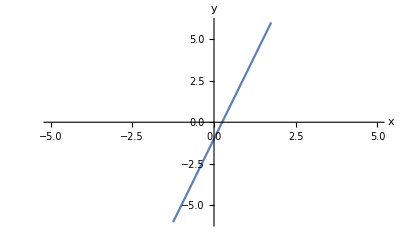

```mathematica
(*the graph of y=4x-1*)
Plot[{4x-1},{x,-5,5}, PlotRange -> {-6,6},AxesLabel->{x,y}]
```

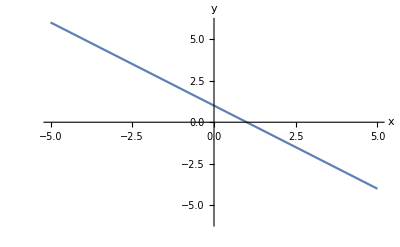

```mathematica
(*the graph of y=-x+1*)
Plot[{-x+1}, {x,-5,5},PlotRange -> {-6,6},AxesLabel->{x,y}]
```

#### Plotting two lines

```mathematica
(*To plot two lines*)
(*
PLot[{Expression1, Expression2},{variable,min,max},PlotRange->{min,max}, AxesLabel->{x,y}]
*)
```

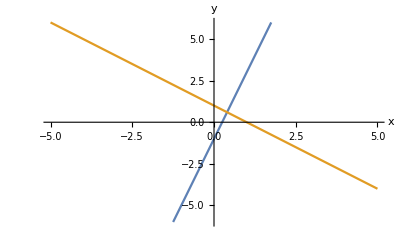

```mathematica
(*the graph of y=4x-1 and y=-x+1*)
Plot[{4x-1, -x+1}, {x,-5,5},PlotRange -> {-6,6},AxesLabel->{x,y}]
```

```mathematica
(*To plot two lines*)
(*
PLot[{Expression1, Expression2},{variable,min,max},PlotRange->{min,max},PlotLegends->"Expressions", AxesLabel->{x,y}]
*)
```

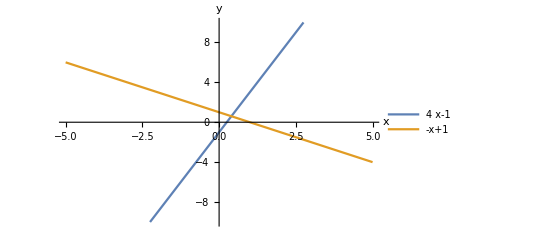

```mathematica
(*the graph of y=4x-1 and y=-x+1 with Axis labels*)
Plot[{4x-1, -x+1}, {x,-5,5},PlotRange->{-10,10},PlotLegends->"Expressions",AxesLabel->{x,y}]
```

## Trigonometry

### Pythagoras

#### Pythagorean theorem

```mathematica
(*To find the value of C use c^2=a^2+b^2 *)
(* [ /.x-> ] When a pronumeral equals to something *)

(*Solve[c^2==a^2+b^2]/.b-> 0 /.a-> 0*)

(*Change 0 to a number*)
```

```mathematica
(*Find the value of C when c^2=a^2+b^2 [b=5,a=3]*)
Solve[c^2==a^2+b^2]/.b-> 5 /.a-> 3
```

{{c→-√34},{c→√34}}

### Exact value

#### Exact value

### Surds

#### Surds

```mathematica
(*for surds*)
-Graphics-          -Graphics-
```

### SIN COS TAN

#### Defining sin cos and tan

```mathematica
(*
If 0 is the angle
opposite...
  hypotenuse...
    adjacent...
-Graphics-
Sin 0 = opposite/hypotenuse
Cos 0 = adjacent/hypotenuse
Tan 0 = opposite/adjacent
*)
```

#### Calculating SIN COS TAN

```mathematica
(* If we know the degree and want to find the fraction we... *)
(*To get [ Sin 0 =opposite/hypotenuse ] *)
(*To get [ Cos 0 = adjacent/hypotenuse ]*)
(*To get [ Tan 0 = opposite/adjacent ]*)
(*Use...]

Sin/Cos/Tan[0 °] 

*)
(*Change the 0 to the a degree*)
```

```mathematica
(*Eg.*)
(*If the degrees is 30 and we are trying to find sin in fraction form*)
Sin[30°]
```

1/2

```mathematica
(*If we know the degree and want to find it in number form we... *)
(*To get [ Sin 0 =opposite/hypotenuse ] *)
(*To get [ Cos 0 = adjacent/hypotenuse ]*)
(*To get [ Tan 0 = opposite/adjacent ]*)
(*Use Sin/Cos/Tan[0 °]//N *)
(*Change the 0 to a degree*)
```

```mathematica
(*Eg.*)
(*If the degrees is 30 and we are trying to find Sin in number form*)
Sin [30°]//N
```

0.5

#### Solving for pro-numerals SIN COS TAN

```mathematica
(*If we know the angle, Sin/Cos/Tan, one of the numbers of the fraction and we are trying to solve for x, we use the formula...*)
(* Use...

Solve[Cos/Sin/Tan[0°]==x/y,x]
*)
(*Change the 0 to a degree*)
```

```mathematica
(*Eg.*)
(*If we know the angle is 30°, is a Cos angle and we know one of the numbers of the fraction, we...*)
Solve[Cos[30 °]==x/8,x]
```

{{x→4 √3}}

```mathematica
(*If we want to know the answer to the above question in number form we...*)
Solve[Cos[30 °]==x/8,x]//N
```

{{x→6.9282}}

```mathematica
(*Eg.*)
(*If we know the angle is 45°, is a Sin angle and we know one of the numbers of the fraction, we.. use*)
Solve[Sin[45°]==12/y,y]
```

{{y→12 √2}}

```mathematica
(*If we want to know the answer to the above question in number form we...*)
Solve[Sin[45°]==12/y,y]//N
```

{{y→16.9706}}

#### Calculating Inverse

```mathematica
(*If we are trying to find the angle of a triangle with only the fraction and the Sin/Cos/Tan *)
(*

	N[ArcSin[0/0]/Degree]
or
   N[ArcCos[0/0]/Degree] 
or
   N[ArcTan[0/0]/Degree]

*)
(*Enter the fraction into the 0/0*)
```

```mathematica
(*Eg.*)
N[ArcSin[1/2]/Degree]
```

30.

#### Sin rule (angle)

```mathematica
(* Used when 2 angles and 2 sides are corresponding to each other in a non-right angled triangles *)
(* To look for the angle in (Sin [A°])/a == (Sin [B°])/b == (Sin [C°])/c use....*)

(* ********



Solve[Sin[A]/a==Sin[B°]/b,Sin[A]]//N

ArcSin[answer]/Degree

******** *)
```

```mathematica
(* Change to degrees from radians, to do that use ArcSin[answer]/Degree *)
Solve[Sin[A]/11==Sin[45°]/8,Sin[A]]//N
ArcSin[0.9722718241315027]/Degree
```

{{Sin[A]→0.972272}}

76.4759

#### Sin rule (side length)

```mathematica
(* Looking for side length *)
(*
To find a in a/(Sin A) = b/(Sin B) use...


 Solve[a/(Sin [A°]) == (b.)/(Sin [B°])]//N
								you have to have the dot behind the number

 or


 (Sin[A°]×b)/Sin[B°]//N

*)
```

```mathematica
(*If we know what b, Sin A and Sin B equals to we use... *)
Solve[a/Sin[49°]==250./Sin[13°]]//N
```

{{a→838.749}}

```mathematica
(*or*)
```

```mathematica
(*If we know what b, Sin A and Sin B equals to we use... *)
(Sin[49°]×250)/Sin[13°]//N
```

838.749

#### Cosine rule (side length)

```mathematica
(* 
   - Used when there are 2 known sides and an angle that is corresponding to the pronumeral 
*)
(* To find the side length, use...
 √(a^2+b^2-2×a×b×Cos[C°])//N
or
 √(a^2+c^2-2×a×c×Cos[B°])//N
or
  √(b^2+c^2-2×b×c×Cos[A°])//N
*)
```

```mathematica
(*Eg.*)
(* When using Cosine rule and we know 2 sides and an angle, we use...


√(a^2+b^2-2×a×b×Cos[C°])//N


a=7  b=5  angle=44
*)
√(7^2+5^2-2×7×5×Cos [44°])//N
```

4.86274

#### Cosine rule (angle)

```mathematica
(*
 - Used when all 3 sides are known and there is an angle that needs to be found 
*)
(*To find the angle, use... 
   N[ArcCos[(a^2+ b^2 - c^2)/(2×a×b)]]/Degree
 or
   N[ArcCos[(b^2+ c^2 - a^2)/(2×b×c)]]/Degree
 or
   N[ArcCos[(a^2+ c^2 - b^2)/(2×a×c)]]/Degree
*)
```

```mathematica
(*Eg.*)
(*
When using Cosine rule and we know all 3 sides, and are trying to find an angle we use...

N[ArcCos[(a^2+ b^2 - c^2)/(2×a×b)]]/Degree

a=7  b=5  c=6
*)

N[ArcCos[(7^2+ 5^2 - 6^2)/(2×7×5)]]/Degree
```

57.1217

## Probability

## Quadratics

### Manipulating equations (Expand, Simplify, Factorise, Substitute)

#### Simplify

```mathematica
(*
To simplify use...
Equation//FullSimplify
or
Equation//Simplify
*)
(*Full simplify and Simplify 
use both and see which is better for the question*)
```

```mathematica
(*Full Simplify
eg.
simplifying (x-1)/(x+1)+(x+1)/(x-1) *)

(x-1)/(x+1)+(x+1)/(x-1)//FullSimplify
```

(2 (1+x^2))/(-1+x^2)

```mathematica
(*Use...
(//Together) to make denominators even before subtracting or adding fractions
eg. 
subtracting (3 x^2-17x+10)/(2 x^2-11x+5) from (6 x^2-x-2)/(2 x^2+9x-5)
*)
(6 x^2-x-2)/(2 x^2+9x-5)-(3 x^2-17x+10)/(2 x^2-11x+5)//FullSimplify//Together
```

((-4+x) (-2+3 x))/((5+x) (-1+2 x))

#### Expand

```mathematica
(*
To expand use...
Expand[Equation]//TraditionalForm
*)
(*Traditional form turns the answer into ax^2+bx+c form*)
```

```mathematica
(*Eg.
Expanding [2((x+1-√(9/2))(x+1+√(9/2)))]*)
Expand[2((x+1-√(9/2))(x+1+√(9/2)))]//TraditionalForm
```

2 x^2+4 x-7

```mathematica
(*Eg.
Expanding [(x-3)^2+20]
*)
Expand[(x-3)^2+20]//TraditionalForm
```

x^2-6 x+29

#### Factorise

```mathematica
(*
To factorise use...
Factor[Equation]//TraditionalForm

(If it doesn't work use...)

Factor[Equation,Extension->All]//TraditionalForm
(It gets the surds out)
*)
```

```mathematica
(*Eg.
	Factorising [6 x^2-x-2]*)
Factor[6 x^2-x-2]//TraditionalForm
```

(2 x+1) (3 x-2)

```mathematica
(*Eg. 
Factorising 6 x^2-x-2 through complete the square*)
Factor[6 x^2-x-2,Extension->All]//TraditionalForm
```

(x-√5+2) (x+√5+2)

#### Substitute

```mathematica
(*
To substitute use...
Equation/.Variable->Number
*)
(* [ /. ] -> When something equals to something *)
```

```mathematica
(* Eg.
Find the value of 2x-7 when x=11 *)
2x-7/.x->11
```

15

### Solving equations

#### Solving for variables

```mathematica
(* 
To solve for a variable use...
Solve[a x^2+b x+c==0,x]

*)
(*  [ ,x  ] shows that it is finding x
   {} means no real solutions          *)
```

```mathematica
Solve[x^2-4==0,x]
```

{{x→-2},{x→2}}

```mathematica
Solve[x^2-6x+9==0,x]
```

{{x→3},{x→3}}

```mathematica
(*
To solve for real numbers use add... 
[ Reals ] at the end to solve for real number
*)
Solve[3 x^2+5x+4==0,x,Reals]
```

{}

#### Solving inequalities

```mathematica
(*
To solve an inequality use...
Reduce[Inequality, x]



x∈Reals -> x is an element of reals which means x is a real number
*)
```

```mathematica
(*Eg.
solving x^2+4>4x as an inequality*)

Reduce[x^2+4>4x,x]
(*x<2||x>2
same as -> x<2 or x>2 
or      -> x<2 U x>2*)
```

x<2||x>2

```mathematica
(*Eg.
solving 5 x^2-10x+5>0 as an inequality*)
Reduce[5 x^2-10x+5>0,x]
(*x<1||x>1
same as -> x<1 or x>1 
or      -> x<1 U x>1*)
```

x<1||x>1

```mathematica
(*Eg.
solving 5 x^2-10x+5<0 as an inequality*)
Reduce[5 x^2-10x+5<0,x]
(*False -> No real value*)
```

False

```mathematica
(*Eg.
solving -x^2+5x-6>=0 as an inequality*)
Reduce [-x^2+5x-6>=0,x]
```

2≤x≤3

#### Solving for x intercept

```mathematica
(*Eg.
x intercept of y=-2x+4 *)
Solve[0==-2x+4,x]
```

{{x→2}}

#### Solving for y intercept

```mathematica
(*Eg.
y intercept of  y=-2x+4
*)
y=-2(0)+4/.x->0
```

4

### Plotting parabolas

#### Plotting single parabolas

```mathematica
(*to plot a single parabola, use...

Plot[{Equation},{x,θ,θ},PlotRange->{θ,θ}] 

θ=number
change θ to the numbers for the range you want
{x,θ,θ} -> x axis range
PlotRange->{θ,θ} -> y axis range
*)
```

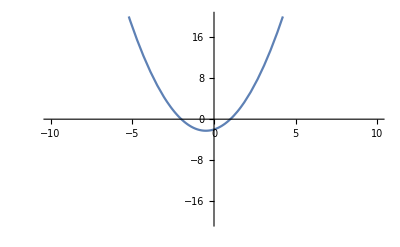

```mathematica
(*Eg*)
Plot[{x^2+x-2},{x,-10,10},PlotRange->{-20,20}]
(*PlotRange = Y axis range*)
```

#### Plotting multiple parabolas

```mathematica
(*to plot multiple parabolas, use...

Plot[{Equation1,Equation2,Equation3},{x,θ,θ},
PlotRange->θ,PlotLegends->"Expressions"]

θ=number
change θ to the numbers for the range you want
{x,θ,θ} -> x axis range
PlotRange->{θ} -> Y Axis range
*)
```

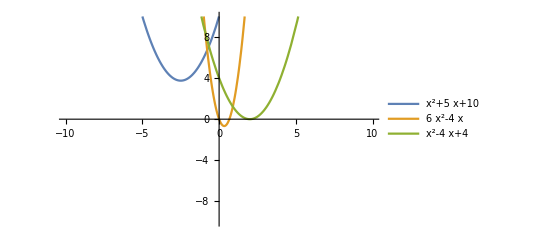

```mathematica
(*Eg*)
Plot[{x^2+5x+10,6 x^2-4x,x^2-4x+4},{x,-10,10},
PlotRange->10,PlotLegends->"Expressions"]
```

#### Manipulating plots

```mathematica
(*Change the y-axis*)
Manipulate[Plot[x^2+k,{x,-10,10},PlotRange->{-20,20}],{k,-5,5}]
```

### Finding the discriminant

```mathematica
(*
the number inside the square root of the quadratic formula ( b^2-4ac )
-Graphics-
 
To find the discrimant of an equation use...
		Discriminant[ax^2+bx+c,x]
*)
```

```mathematica
(*Eg.
discriminant of x^2+4x-5
*)
Discriminant[x^2+4x-5,x]
```

36

```mathematica
(*Eg.
discriminant of 2 x^2+6x+k
*)
Discriminant[2 x^2+6x+k,x]
```

-4 (-9+2 k)

### Completing the square

```mathematica
(*
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
[press shift enter]
compsq[a,b,c]

a,b,c -> change to corresponding number
*)
```

```mathematica
(*Eg.
complete the square on 1 x^2+4x-1
*)
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
compsq[1,4,-1]
```

(x+2)^2-5

```mathematica
(*Eg.
complete the square on 4 x^2+8/5 x-1/5
*)
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
compsq[4,8/5,-1/5]
```

4 (x+1/5)^2-9/25

### Finding quadratic rule

#### 3 given points

```mathematica
(* To find the quadratic rule from 3 different points, 
	use....
	 	f[x_]:=a x^2+b x+c
		Solve[{f[x1]==y1,f[x2]==y2,f[x3]==y3},{a,b,c}]

coordinates: (x1,y1), (x2,y2) and (x3,y3)
*)
```

```mathematica
(*Eg.
	Finding the rule of the quadratic that goes through the coordinates (1,4), (-1,10) and (3,2)*)

f[x_]:=a x^2+b x+c
Solve[{f[1]==-4,f[-1]==10,f[3]==-2},{a,b,c}]
```

{{a→2,b→-7,c→1}}

#### Intercept form

```mathematica
(*To find rule when you have two x intercepts use...
	Solve[y==a(x-x1)(x-x2),a]/.x->0

x->0  -> x value being subbed in
 0  -> number
x1  -> x intercept 1
x2  -> x intercept 2
 y  -> y value being subbed in
*)
```

```mathematica
(*Eg.
Rule when the two x intercepts are (2,0) and (-3,0) and the point being subbed in is (5,4)*)
Solve[4==a(x-2)(x+3),a]/.x->5
```

{{a→1/6}}

#### Turning point

```mathematica
(*To find rule when you have a turning point use...
Solve[y==a(x-x1)^2+y1,a]/.x->0


x1 -> x value of turning point
y1 -> y value of turning point

Sub in another known point
	x->0  -> x value of second known point
  y  -> y value of second known point
*)
```

```mathematica
(*Eg.
Rule when turning point is (2,6)and the second known point is (5,4)*)
Solve[4==a(x-2)^2+6,a]/.x->5
```

{{a→-2/9}}

### Finding the turning point

#### Completing the square method

```mathematica
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
compsq[4,10,7]
(*x coordinate for turning point form is flipped*)
      |
5/4 ->= - 5/4
```

4 (x+5/4)^2+3/4

```mathematica
(*
TP:(-5/4,3/4)
*)
```

### Number of intersections

```mathematica
(*
Discriminant= greater than 0 / >0 -> two points of intersection
Discriminant=0 -> one point of intersection
   Discriminant= less than 0 / <0 -> no points of intersection
*)
```

### Points of intersection

```mathematica
(*
The points of intersection between 
y==5 x^2-7x-8   and   y==x+1
*)
Solve[{y==5 x^2-7x-8,y==x+1},{x,y}]
```

{{x→1/5 (4-√61),y→1/5 (9-√61)},{x→1/5 (4+√61),y→1/5 (9+√61)}}

```mathematica
(*
((4-√61)/5,(9-√61)/5) and ((4+√61)/5,(9+√61)/5)
*)
```